```mathematica
ClearAll["Global`*"]
```

```mathematica
<<"/Users/alexdeich/thesis/code/mine/ThesisTools.m"
```

#### Calculate force on one particle

G[f_,i_] returns the force on the particle i whose position in state space is given in f , which is an array (created above as InitVecs.)

```mathematica
G[f_,i_]:=Module[{j,x1,x2,y1,y2,distance2,jforce,jforcedir,totalforce,forces},
forces = Table[{0.,0.},Nparticles];
x1 = f[[i,1,1]];
y1 = f[[i,1,2]];
For [j=1,j≤ Nparticles,j++,
If[j≠ i,
x2 = f[[j,1,1]];
y2 = f[[j,1,2]];
distance2 = ((x2-x1)^2+(y2-y1)^2);
(*If[distance2<epsilon,
Print["Something collided"];
Abort[];
];*)
jforce = 1/distance2;
jforcedir = {x2-x1,y2-y1}/Sqrt[distance2];
forces[[j]] = jforce*jforcedir;
];
];
Return[Total[forces]];
]
```

#### Get force on every particle

GetForces[state_] returns an array with size Nparticles with the force information for each particle in x and y: {{fx},{fy}}

```mathematica
GetForces[state_]:=Module[{particle,totalforces},
totalforces = Table[{},Nparticles];
For[particle=1,particle≤Nparticles,particle++,
totalforces[[particle]]=G[state,particle]
];
Return[totalforces]
]
```

For a sanity check, if Nparticles==2, the two forces returned should be equal and opposite.

```mathematica
GetForces[InitVecs]
```

{{-0.0220971,-0.0220971},{0.0220971,0.0220971}}

#### Initilialize potentially usefull things

Initialize state vector with {{x,y},{xd,yd}}

```mathematica
(*InitVecs = Table[{{RandomReal[{-2,2}],RandomReal[{-2,2}]},{0,RandomReal[{-0.5,0.5}]}},Nparticles];*)
timesteps = 10000;
dt = .001;
mass = 100;
epsilon = 0.000001;
InitVecs = {{{2,2},{0,-3}},{{-2,-2},{0,3}}};
wholestory = Table[0,timesteps];
Nparticles = Length[InitVecs];
```

#### Time evolution

```mathematica
StateVecs = InitVecs;
For[timestep = 1,timestep≤timesteps,timestep++,
currentforces = GetForces[StateVecs];
NewState = Table[{{0,0},{0,0}},Nparticles];
For[i=1,i≤ Nparticles,i++,
oldx = StateVecs[[i,1,1]];
oldy = StateVecs[[i,1,2]];
oldxd = StateVecs[[i,2,1]];
oldyd = StateVecs[[i,2,2]];
xdd= currentforces[[i,1]]*mass;
ydd = currentforces[[i,2]]*mass;
newx = oldxd * dt + oldx;
newy = oldyd * dt + oldy;
newxd = xdd*dt + oldxd;
newyd = ydd*dt + oldyd;
NewState[[i]][[1,1]] = newx;
NewState[[i]][[1,2]] = newy;
NewState[[i]][[2,1]] = newxd;
NewState[[i]][[2,2]] = newyd;
];
StateVecs = NewState;
(*Print[timestep," ",StateVecs];*)
wholestory[[timestep]] = StateVecs;
]
```

#### Plotting

```mathematica
colors = {Blue,Red,Orange,Green};
```

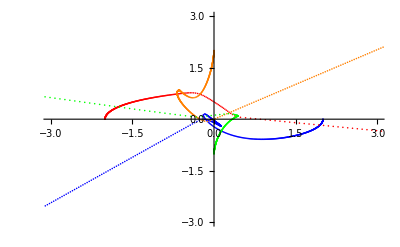

```mathematica
xyplots = Table[0,Nparticles];
For[particle=1,particle≤Nparticles,particle++,
xyplots[[particle]] = ListPlot[Table[{wholestory[[t,particle,1,1]],wholestory[[t,particle,1,2]]},{t,1,timesteps}],PlotRange->{{-3,3},{-3,3}},PlotStyle->{colors[[particle]]}];
]
Show[xyplots]
```

#### To do

• Optimize, allow for collisions, particle clumping
• How to combine with Kerr RK4?!?!?!?